```mathematica
Subscript[G, ∞]=1 - Sum[Subscript[G, i], {i, 1, n}];
Yt = Sum[Subscript[G, i]*Exp[-t / Subscript[τ, i]], {i, 1, n}] + Subscript[G, ∞];
Ys = LaplaceTransform[Yt, t, s];
```

```mathematica
Js = 1 / s^2 / Ys;
Jt2 = InverseLaplaceTransform[Js/.n->2, s, t]
```

1/(1-G_1-G_2)+(-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 τ_1+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 τ_1+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2 τ_1-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2 τ_1-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 G_2 τ_1+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 G_2 τ_1-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2^2 τ_1+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2^2 τ_1+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 τ_2-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 τ_2-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1^2 τ_2+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1^2 τ_2-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2 τ_2+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2 τ_2-ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 G_2 τ_2+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 G_2 τ_2+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 √(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2)+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_1 √(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2)+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)-(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2 √(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2)+ⅇ^(t (-1/(2 τ_1)+G_1/(2 τ_1)-1/(2 τ_2)+G_2/(2 τ_2)+(√(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 τ_1 τ_2))) G_2 √(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))/(2 (-1+G_1+G_2) √(-4 (1-G_1-G_2) τ_1 τ_2+(τ_1-G_2 τ_1+τ_2-G_1 τ_2)^2))

```mathematica
Jt2 /. {Subscript[G, 1]->.3, Subscript[G, 2]-> .3, Subscript[τ, 1]->.3, Subscript[τ, 2]->1}
(*Jt2 /. (1-Subscript[G, 1]-Subscript[G, 2]) -> Subscript[G, inf]*)
```

2.5-2.11864 (0.12 ⅇ^(-2.5 t)+0.588 ⅇ^(-0.533333 t))

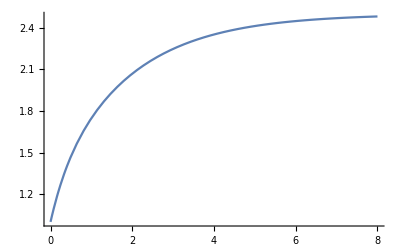

```mathematica
Plot[2.5-2.1186440677966103 (0.11999999999999994 ⅇ^(-2.5 t)+0.5880000000000001 ⅇ^(-0.5333333333333334 t)),{t,0,8}]
```